0.+2. x

8.+6.9502×10^-17 x

-2952.58

FittedModel::bdfit: The sum of squared errors is not a non-negative number. The model may suffer from significant numerical error or may not be appropriate for the data.

-3534.27

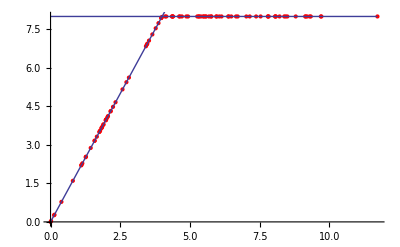

```mathematica
data=Import["C:\\Users\\Stefano\\Desktop\\Programmazione\\Python\\Hackerrank\\LaptopBatteryLife.txt","Table"];
data1=Select[data,#[[1]]<4&];
data2=Select[data,#[[1]]>=4&];
model =LinearModelFit[data1, {1,x},x];
model2 =LinearModelFit[data2, {1,x},x];
Normal[model]
Normal[model2]
model["AIC"]
model2["AIC"]
Show[ListPlot[data, PlotStyle->Red], Plot[Normal[model], {x, Min[data[[All,1]]], Max[data[[All,1]]]}],Plot[Normal[model2], {x, Min[data[[All,1]]], Max[data[[All,1]]]}]]
```